```mathematica
β1[ω_,δ_,t_,ϵ_]:=β1[ω,δ,t,ϵ]=(ω+ⅈ*δ-ϵ)IdentityMatrix[1]
```

```mathematica
T2[t_]:=T2[t]= t*IdentityMatrix[1]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=Module[{J=Inverse[β1[ω,0.0001,1,0]],B:=Inverse[β1[ω,0.0001,1,0]],T:=T2[1]},Do[J=Inverse[IdentityMatrix[1]-B.T.J.T].B,100000];J=J]
```

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,2,0.01]}]
```

```mathematica
leads[1]
```

{{{0.-1.01351 ⅈ}},{{-0.00148693-0.98822 ⅈ}},{{0.0216281-1.00679 ⅈ}},{{0.00153493-0.999824 ⅈ}},{{0.0311001-0.992233 ⅈ}},{{0.0203637-1.01235 ⅈ}},{{0.0254585-0.986943 ⅈ}},{{0.047156-1.00512 ⅈ}},{{0.0276311-1.00442 ⅈ}},{{0.0476506-0.9859 ⅈ}},{{0.0603091-1.0073 ⅈ}},{{0.0431882-1.00476 ⅈ}},{{0.0565836-0.985353 ⅈ}},{{0.0780571-0.995392 ⅈ}},{{0.0734266-1.01041 ⅈ}},{{0.063384-1.0036 ⅈ}},{{0.0692621-0.989122 ⅈ}},{{0.0845439-0.983243 ⅈ}},{{0.0981207-0.985641 ⅈ}},{{0.106929-0.990082 ⅈ}},{{0.112839-0.992586 ⅈ}},{{0.117765-0.991909 ⅈ}},{{0.121518-0.987972 ⅈ}},{{0.121603-0.982269 ⅈ}},{{0.116094-0.980513 ⅈ}},{{0.112225-0.990749 ⅈ}},{{0.127544-1.00411 ⅈ}},{{0.147713-0.990042 ⅈ}},{{0.132464-0.979963 ⅈ}},{{0.145276-1.0021 ⅈ}},{{0.152753-0.976442 ⅈ}},{{0.153951-1.00042 ⅈ}},{{0.154505-0.975959 ⅈ}},{{0.177272-0.988015 ⅈ}},{{0.16594-0.997119 ⅈ}},{{0.162765-0.983614 ⅈ}},{{0.172645-0.973954 ⅈ}},{{0.181711-0.971087 ⅈ}},{{0.185481-0.970627 ⅈ}},{{0.184969-0.974256 ⅈ}},{{0.189832-0.986033 ⅈ}},{{0.212215-0.988152 ⅈ}},{{0.213248-0.966429 ⅈ}},{{0.207797-0.985829 ⅈ}},{{0.224992-0.965062 ⅈ}},{{0.228936-0.985188 ⅈ}},{{0.218726-0.975132 ⅈ}},{{0.228284-0.962866 ⅈ}},{{0.238136-0.95969 ⅈ}},{{0.241193-0.959039 ⅈ}},{{0.239684-0.964204 ⅈ}},{{0.250759-0.977088 ⅈ}},{{0.270393-0.962417 ⅈ}},{{0.254254-0.965407 ⅈ}},{{0.278201-0.956018 ⅈ}},{{0.279555-0.971018 ⅈ}},{{0.273985-0.968626 ⅈ}},{{0.277089-0.965306 ⅈ}},{{0.286947-0.966875 ⅈ}},{{0.304065-0.960147 ⅈ}},{{0.298225-0.944001 ⅈ}},{{0.306288-0.962261 ⅈ}},{{0.301906-0.945039 ⅈ}},{{0.319106-0.940224 ⅈ}},{{0.327646-0.941516 ⅈ}},{{0.329232-0.937146 ⅈ}},{{0.32232-0.938442 ⅈ}},{{0.336957-0.951346 ⅈ}},{{0.335841-0.932171 ⅈ}},{{0.353937-0.936881 ⅈ}},{{0.357257-0.942049 ⅈ}},{{0.363231-0.938173 ⅈ}},{{0.3651-0.925816 ⅈ}},{{0.356556-0.933002 ⅈ}},{{0.37662-0.923645 ⅈ}},{{0.380363-0.933495 ⅈ}},{{0.382513-0.932886 ⅈ}},{{0.392405-0.926357 ⅈ}},{{0.389734-0.912733 ⅈ}},{{0.396435-0.926482 ⅈ}},{{0.392151-0.916726 ⅈ}},{{0.397838-0.911389 ⅈ}},{{0.403397-0.915848 ⅈ}},{{0.422002-0.912336 ⅈ}},{{0.412696-0.908478 ⅈ}},{{0.421727-0.89872 ⅈ}},{{0.425643-0.89718 ⅈ}},{{0.429805-0.905095 ⅈ}},{{0.445003-0.893312 ⅈ}},{{0.449289-0.900676 ⅈ}},{{0.453824-0.898377 ⅈ}},{{0.460474-0.887024 ⅈ}},{{0.454459-0.891068 ⅈ}},{{0.461591-0.880038 ⅈ}},{{0.465918-0.878057 ⅈ}},{{0.471816-0.885053 ⅈ}},{{0.480488-0.871389 ⅈ}},{{0.489761-0.871301 ⅈ}},{{0.490409-0.86608 ⅈ}},{{0.492519-0.873789 ⅈ}},{{0.495324-0.863275 ⅈ}},{{0.49986-0.861831 ⅈ}},{{0.512206-0.86477 ⅈ}},{{0.50995-0.85708 ⅈ}},{{0.515069-0.854142 ⅈ}},{{0.527443-0.855157 ⅈ}},{{0.525313-0.848219 ⅈ}},{{0.530496-0.845619 ⅈ}},{{0.543588-0.844175 ⅈ}},{{0.542098-0.841613 ⅈ}},{{0.549582-0.839302 ⅈ}},{{0.555927-0.827846 ⅈ}},{{0.563523-0.826699 ⅈ}},{{0.563241-0.821606 ⅈ}},{{0.573666-0.822135 ⅈ}},{{0.578487-0.817243 ⅈ}},{{0.576465-0.81493 ⅈ}},{{0.581955-0.80939 ⅈ}},{{0.590277-0.810645 ⅈ}},{{0.591944-0.804724 ⅈ}},{{0.600881-0.802904 ⅈ}},{{0.601982-0.796331 ⅈ}},{{0.609003-0.795073 ⅈ}},{{0.613041-0.786472 ⅈ}},{{0.617392-0.785318 ⅈ}},{{0.625253-0.778016 ⅈ}},{{0.627653-0.77563 ⅈ}},{{0.635923-0.770282 ⅈ}},{{0.637694-0.767967 ⅈ}},{{0.643921-0.762195 ⅈ}},{{0.650044-0.761995 ⅈ}},{{0.655262-0.757579 ⅈ}},{{0.658425-0.750037 ⅈ}},{{0.663747-0.748193 ⅈ}},{{0.668197-0.742455 ⅈ}},{{0.676579-0.737336 ⅈ}},{{0.680074-0.731567 ⅈ}},{{0.686054-0.727442 ⅈ}},{{0.689587-0.725161 ⅈ}},{{0.696311-0.718772 ⅈ}},{{0.701097-0.71348 ⅈ}},{{0.705943-0.709885 ⅈ}},{{0.708789-0.7042 ⅈ}},{{0.715921-0.69958 ⅈ}},{{0.720428-0.693012 ⅈ}},{{0.724769-0.687747 ⅈ}},{{0.729837-0.682496 ⅈ}},{{0.73536-0.677275 ⅈ}},{{0.740739-0.672522 ⅈ}},{{0.745228-0.667699 ⅈ}},{{0.749432-0.66185 ⅈ}},{{0.754331-0.655488 ⅈ}},{{0.75958-0.649404 ⅈ}},{{0.764598-0.643554 ⅈ}},{{0.769436-0.637996 ⅈ}},{{0.775145-0.632326 ⅈ}},{{0.779651-0.625417 ⅈ}},{{0.785102-0.619096 ⅈ}},{{0.789816-0.612726 ⅈ}},{{0.795023-0.606866 ⅈ}},{{0.799848-0.600225 ⅈ}},{{0.805157-0.593095 ⅈ}},{{0.810163-0.586382 ⅈ}},{{0.814723-0.579427 ⅈ}},{{0.819864-0.572486 ⅈ}},{{0.824805-0.56519 ⅈ}},{{0.829838-0.557601 ⅈ}},{{0.835049-0.550199 ⅈ}},{{0.839854-0.54262 ⅈ}},{{0.844856-0.53465 ⅈ}},{{0.849892-0.526658 ⅈ}},{{0.854854-0.518599 ⅈ}},{{0.85992-0.510188 ⅈ}},{{0.864867-0.501722 ⅈ}},{{0.869873-0.492999 ⅈ}},{{0.874889-0.484049 ⅈ}},{{0.879897-0.4749 ⅈ}},{{0.884885-0.465545 ⅈ}},{{0.889903-0.455895 ⅈ}},{{0.894895-0.446027 ⅈ}},{{0.899902-0.435833 ⅈ}},{{0.9049-0.425364 ⅈ}},{{0.909886-0.414556 ⅈ}},{{0.91489-0.403405 ⅈ}},{{0.919885-0.391867 ⅈ}},{{0.924878-0.379916 ⅈ}},{{0.929874-0.367509 ⅈ}},{{0.934868-0.354598 ⅈ}},{{0.939862-0.341124 ⅈ}},{{0.944855-0.32702 ⅈ}},{{0.949848-0.3122 ⅈ}},{{0.954839-0.296556 ⅈ}},{{0.959829-0.27995 ⅈ}},{{0.964816-0.2622 ⅈ}},{{0.9698-0.243055 ⅈ}},{{0.974781-0.222155 ⅈ}},{{0.979754-0.198948 ⅈ}},{{0.984715-0.172505 ⅈ}},{{0.989649-0.141018 ⅈ}},{{0.994502-0.0998262 ⅈ}},{{0.992929-0.00702116 ⅈ}}}

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]](*Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,50000];J=J]*)
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[concentration_]:=dist[concentration]=Table[SortBy[Join[RandomSample[Join[s[13,36,13,36]],concentration],RandomSample[Join[s[1,12,1,50],s[37,50,1,50],s[13,36,1,12],s[13,36,37,50]],50-concentration]],First],10000]
```

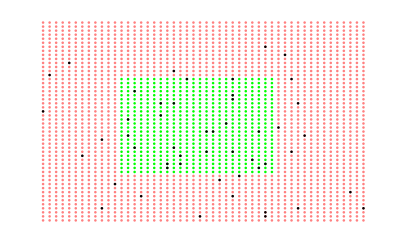

```mathematica
ListPlot[{Join[s[13,36,13,36]],Join[s[1,12,1,50],s[37,50,1,50],s[13,36,1,12],s[13,36,37,50]],dist[25][[30]]},PlotStyle->{Green,Pink,Black},Axes->False]
```

```mathematica
Export["device.pdf",%43]
```

device.pdf

```mathematica
TLD[t_]:=Module[{sizeoflead=1},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,{{50,50}}->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;1,1;;1]]=LEFT[ω,1];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[50;;50,50;;50]]=LEFT[ω,1];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=1},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,sizeoflead].SLLEAD[ω,sizeoflead].T[1,sizeoflead]].g[ω,0.0001,1,0]]
```

```mathematica
device1[0]
```

{{0.-0.00249376 ⅈ,0.997506+0. ⅈ,0.+0.00239401 ⅈ,-0.997506+0. ⅈ,0.-0.00229426 ⅈ,0.997505+0. ⅈ,0.+0.00219451 ⅈ,-0.997505+0. ⅈ,0.-0.00209476 ⅈ,0.997505+0. ⅈ,0.+0.00199501 ⅈ,-0.997505+0. ⅈ,0.-0.00189526 ⅈ,0.997505+0. ⅈ,0.+0.00179551 ⅈ,-0.997504+0. ⅈ,0.-0.00169576 ⅈ,0.997504+0. ⅈ,14,0.-0.000897753 ⅈ,0.997503+0. ⅈ,0.+0.000798002 ⅈ,-0.997503+0. ⅈ,0.-0.000698252 ⅈ,0.997503+0. ⅈ,0.+0.000598502 ⅈ,-0.997503+0. ⅈ,0.-0.000498751 ⅈ,0.997503+0. ⅈ,0.+0.000399001 ⅈ,-0.997503+0. ⅈ,0.-0.000299251 ⅈ,0.997503+0. ⅈ,0.+0.000199501 ⅈ,-0.997503+0. ⅈ,0.-0.0000997503 ⅈ,0.997503+0. ⅈ},48,{1}}
 |  |  |  |

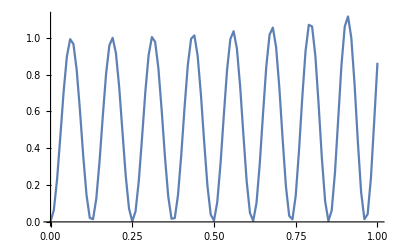

```mathematica
Monitor[ListLinePlot[Table[{ω,-Im[device1[ω][[1,1]]]},{ω,Range[0,1,0.01]}]],ω]
```

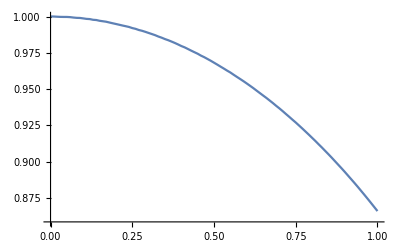

```mathematica
ListLinePlot[Table[{ω,-Im[LEFT[ω,1][[1,1]]]},{ω,Range[0,1,0.01]}]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,concentration_,number_]:= Module[{sizeoflead=1},
recurs=Module[{J1= device1[ω]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,50}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,50}];J]],{unitcell,50}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
CA[0,0.0001,1,0,1,25,1]
```

0.614208

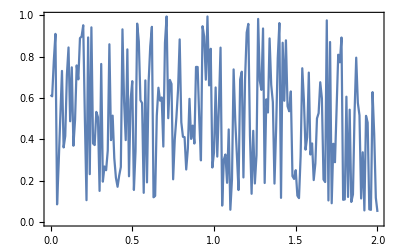

```mathematica
Monitor[ListLinePlot[Table[{Ω,CA[Ω,0.0001,1,0,1,25,1]},{Ω,Range[0,2,0.01]}],Frame->True],Ω]
```

```mathematica
Export["transmission.pdf",%40]
```

transmission.pdf

```mathematica
Monitor[Table[Monitor[Table[Mean[Monitor[ParallelTable[CA[ω,0.0001,1,0,1,conc,n],{n,2500}],n]],{conc,10,40,5}],conc],{ω,Range[0.1,1,0.1]}],ω]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{84672.2-85564.5 ⅈ,-260640.+287605. ⅈ,212256.-239880. ⅈ,52400.9-58887.5 ⅈ,-90383.1+99246.2 ⅈ,-86977.6+109450. ⅈ,102020.-123131. ⅈ,22275.5-33203.7 ⅈ,-98284.8+120788. ⅈ,197365.-217704. ⅈ,«40»},{-84676.+85562.1 ⅈ,260651.-287597. ⅈ,-212265.+239873. ⅈ,-52401.+58885.8 ⅈ,90385.4-99243.3 ⅈ,86980.9-109447. ⅈ,-102024.+123128. ⅈ,-22277.3+33202.9 ⅈ,98290.7-120785. ⅈ,-197375.+217698. ⅈ,«40»},«8»,«40»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{37487.8+65739.8 ⅈ,-53814.7-101269. ⅈ,48014.+90322.6 ⅈ,-22736.5-37835.7 ⅈ,2710.13+2671.92 ⅈ,-20205.4-33425.8 ⅈ,8251.72+6934.5 ⅈ,30148.6+56311. ⅈ,-53583.8-86648.6 ⅈ,65515.+113183. ⅈ,«40»},{-37491.6-65736.9 ⅈ,53821.4+101265. ⅈ,-48018.6-90318.9 ⅈ,22738.4+37833.6 ⅈ,-2710.14-2671.53 ⅈ,20206.7+33424.1 ⅈ,-8252.15-6933.7 ⅈ,-30151.1-56308.6 ⅈ,53588.6+86644. ⅈ,-65521.9-113177. ⅈ,«40»},«8»,«40»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{422281.-122551. ⅈ,-342866.+100231. ⅈ,-100746.+28092.2 ⅈ,255484.-74696.5 ⅈ,-107997.+32322.1 ⅈ,-175512.+50664.1 ⅈ,305672.-89196.5 ⅈ,-105579.+31510.3 ⅈ,-151518.+44293.6 ⅈ,111379.-35186.9 ⅈ,«40»},{-422267.+122598. ⅈ,342856.-100268. ⅈ,100743.-28103.7 ⅈ,-255476.+74724.5 ⅈ,107993.-32333.7 ⅈ,175506.-50683.4 ⅈ,-305663.+89229.9 ⅈ,105575.-31521.4 ⅈ,151513.-44310.5 ⅈ,-111375.+35198.6 ⅈ,«40»},«8»,«40»} may contain significant numerical errors.

{{0.706829,0.685292,0.659866,0.660035,0.641986,0.620365,0.610965},{0.671695,0.654499,0.637336,0.62612,0.613581,0.604317,0.593016},{0.612686,0.603686,0.600568,0.587146,0.586723,0.576476,0.573234},{0.554351,0.548134,0.552799,0.545623,0.542491,0.536907,0.537919},{0.54392,0.532273,0.530747,0.539065,0.542609,0.524301,0.532952},{0.538762,0.553261,0.54849,0.534377,0.532645,0.523451,0.531984},{0.549821,0.547843,0.531225,0.526481,0.531619,0.507969,0.518918},{0.542759,0.531327,0.526433,0.525508,0.507127,0.511082,0.507421},{0.500855,0.494355,0.490089,0.482897,0.490956,0.49307,0.48437},{0.4726,0.475484,0.472536,0.473299,0.469883,0.462239,0.467247}}

```mathematica
Dimensions[Range[1,10,1]]
```

{10}

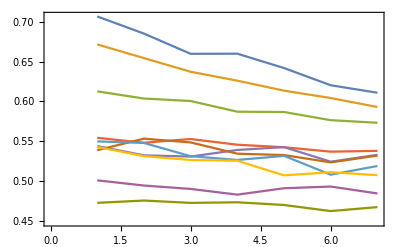

```mathematica
ListLinePlot[%68,Frame->True]
```